```mathematica
Fspring[s_]:=(b Em h^3 s)/(Ls^3 4)
```

```mathematica
Ls = 0.25;
h = 0.6*10^-3;
b=2.8*10^-2;
Em = 100*10^9;
M = (150.74*10^-3)/1.03*Ls; (*масса колебающегося конца линейки*)
m = 0; (*масса грузика на конце линейки, при m=0 грузика нет и есть только собственные колебания линейки*)
l=0.24; (*удаление грузика от оси вращения*)
```

```mathematica
Ioverall = (M Ls^2)/3+m l^2
```

0.000762237

```mathematica
solution = DSolve[{α''[t] == -Fspring[α[t] * Ls]/Ioverall, α[0] == 0.1, α'[0] ==0},α[t], t]
```

{{α[t]→0.1 Cos[56.3366 t]}}

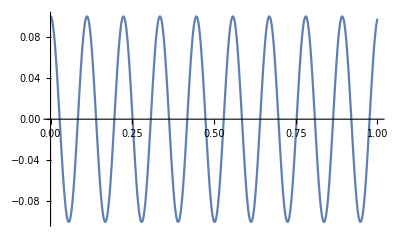

```mathematica
Plot[solution[[1, 1, 2]], {t, 0, 1}]
```

```mathematica
56.34/(2Pi)
```

8.96679